```mathematica
Clear["Global`*"]
```

# Alternative Ansatz

## Cory Aitchison - February 2022

Consider an ansatz of a weighted average of u0 + some function that satisfies the DE near the origin.

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f, g, h, i, j, k};
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

### Solutions

```mathematica
SubAnswers[eq_, n_] := SubAnswers[eq /. answer[n-1], n-1];
SubAnswers[eq_, 1] := eq;

GetEquation[n_]:= LDE[x |-> Sum[u[k][x], {k, 0, n}]] + NDE[x |-> Sum[u[k][x], {k, 0, n-1}]];
GetSolution[n_] := AnalyticSolve[SubAnswers[GetEquation[n], n], n, x, σ, letters[[n]]] // FullSimplify;

GetLinear[ans_] := Coefficient[(Last /@List @@@ ans)/. B->0 ,A, 1]A + Coefficient[(Last /@List @@@ ans)/. A->0 ,B, 1]B;
ShowLinear[n_]:=(x |-> PadRight[x, 2 + 2n,  _])/@GetLinear/@ (answer[#]&/@Range[1,n]) // Transpose// MatrixForm ;

ShowValues[n_] := (x |-> PadRight[x, 2 + 2n, _])/@((answer[#]/. param /. estimates)&/@Range[1,n])//Transpose//MatrixForm;

FinalFunction[n_] := SubAnswers[Sum[u[k][x], {k, 0, n}], n+1]/.param  /. estimates;
FinalFunction[0] := u[0][x] /. param /. estimates;
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
taylorests[0] = {A->0.033327514775158475,B->1.153359200278144};
taylorests[1] = {A->0.24242264239512362,B->0.8985343791605391};
taylorests[3] = {A->0.33494186742400267,B->0.6945601303275413};
```

```mathematica
DumpGet["/Users/cory/Sync/USYD/Denison/Mathematica/answerSave.mx"]
```

### Long data

```mathematica
data = Import["/Users/cory/Sync/USYD/Denison/MATLAB/PQS analytic/PureQuartic.csv"];
```

```mathematica
fdata = Interpolation[data];
fdata4[x_] := 4σ^4 fdata[x]+ Γ fdata[x]^3 /. param;
```

## New function

```mathematica
sss[x_]:=Sin[σ x] Sinh[2 σ x] Csch[(3σ x)/2]^2;
ccc[x_]:=Cos[σ x] Cosh[2σ x] Sech[(3σ x)/2]^2;
w[x_] := p0 ccc[x]+ p1 sss[x];
```

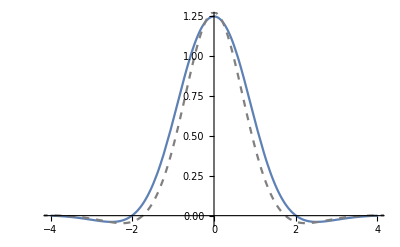

```mathematica
Show[Plot[1.4 sss[x] /. param, {x,-4,4}], ListLinePlot[data, PlotStyle->{Gray, Dashed}, PlotRange->{{-4,4},All}]]
```

### Derivatives

The fourth derivative does not have the same shape  as the data:

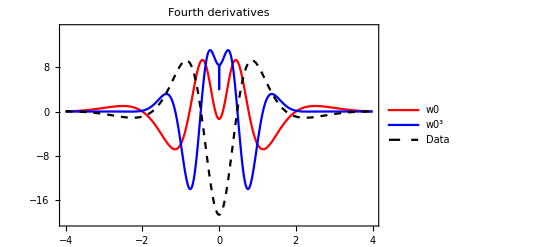

```mathematica
Plot[{D[1.5sss[x]  /. param, {x,4}] /. {x -> t}, D[0.5sss[x]^3  /. param, {x,4}] /. {x -> t}, fdata4[t]}, {t,-4,4}, PlotLegends->{w0, w0^3, Data}, Frame -> True, PlotRange -> {{-4,4}, {-20,15}}, PlotLabel->"Fourth derivatives", PlotStyle->{{Thick, Red}, {Thick, Blue}, {Dashed, Black}}]
```

### Order

Can we express the fourth derivative in terms of their 3rd and 1st powers, to some order?

```mathematica
notrig = {
	Cosh[t_] -> cosh[t], Sinh[t_]->sinh[t],
	Tanh[t_] -> sinh[t] / cosh[t], Coth[t_] -> cosh[t] / sinh[t], 
	Sech[t_] -> 1/cosh[t],  Csch[t_] -> 1/sinh[t]
};
doubletrig = {
sinh[2σ x] -> 4cosh[σ x/2]^3 sinh[σ x/2] + 4 cosh[σ x/2]sinh[σ x/2]^3,
cosh[2σ x] -> cosh[σ x/2]^3 + 6 cosh[σ x/2]^2 sinh[σ x/2]^2 + sinh[σ x/2]^4,
sinh[3 σ x/2] -> 3cosh[σ x/2]^2 sinh[σ x/2] + sinh[σ x/2]^3,
cosh[3σ x/2] -> cosh[σ x/2]^3 + 3cosh[σ x/2] sinh[σ x/2]^2
};
htrigident = {
	cosh[t_]^k_-> (1+sinh[t]^2)^(Floor[k/2]) cosh[t]^(Mod[k,2])
};
trigident = {
	Cos[x σ]^k_-> (1-Sin[x σ]^2)^(Floor[k/2]) Cos[x σ]^(Mod[k,2])
};
```

```mathematica
LDE[x |-> A ccc[x] + B sss[x]] //. notrig //. doubletrig //. htrigident//Expand  // Together
```

-((3 (-216 B σ^4 cosh[(x σ)/2]^7 Sin[x σ]+864 B σ^4 cosh[(x σ)/2]^8 Sin[x σ]-1188 B σ^4 cosh[(x σ)/2]^9 Sin[x σ]+432 B σ^4 cosh[(x σ)/2]^10 Sin[x σ]-216 B σ^4 cosh[(x σ)/2]^11 Sin[x σ]-648 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]+1728 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]-1296 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]+864 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]-2376 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^2+26640 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^2-41688 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^2+16560 B σ^4 cosh[(x σ)/2]^10 Sin[x σ] sinh[(x σ)/2]^2-9072 B σ^4 cosh[(x σ)/2]^11 Sin[x σ] sinh[(x σ)/2]^2-3888 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^3-19224 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^3+55872 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^3-46224 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]^3+33984 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]^3+43416 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^4+362160 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^4-651024 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^4+285696 B σ^4 cosh[(x σ)/2]^10 Sin[x σ] sinh[(x σ)/2]^4-172800 B σ^4 cosh[(x σ)/2]^11 Sin[x σ] sinh[(x σ)/2]^4-39366 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^5+39366 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^5+1458 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^5-115992 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^5-254736 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^5+790992 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^5-738432 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]^5+603648 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]^5+314928 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^6-209952 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^6-192456 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^6+46656 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^6+1140768 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^6+2854656 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^6-5942016 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^6+2923776 B σ^4 cosh[(x σ)/2]^10 Sin[x σ] sinh[(x σ)/2]^6-1969920 B σ^4 cosh[(x σ)/2]^11 Sin[x σ] sinh[(x σ)/2]^6-236196 A σ^4 Cos[x σ] sinh[(x σ)/2]^7+1594323 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^7-2283228 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^7-39366 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^7+148716 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^7+36450 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^7-1546992 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^7-1998720 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^7+6376320 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^7-6960384 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]^7+6386688 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]^7+1889568 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^8+3096792 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^8-1154736 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^8-4298184 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^8+1213056 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^8+11361024 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^8+14454016 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^8-34953984 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^8+19685376 B σ^4 cosh[(x σ)/2]^10 Sin[x σ] sinh[(x σ)/2]^8-14929920 B σ^4 cosh[(x σ)/2]^11 Sin[x σ] sinh[(x σ)/2]^8+9526572 A σ^4 Cos[x σ] sinh[(x σ)/2]^9+18180531 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^9-27490590 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^9-9106668 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^9+3486078 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^9+400464 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^9-12228480 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^9-10401024 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^9+31598848 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^9-42909696 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]^9+44679168 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]^9+18895680 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^10+3621672 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^10+23007240 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^10-42083712 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^10+13934592 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^10+66017280 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^10+49381376 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^10-137465856 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^10+91348992 B σ^4 cosh[(x σ)/2]^10 Sin[x σ] sinh[(x σ)/2]^10-78962688 B σ^4 cosh[(x σ)/2]^11 Sin[x σ] sinh[(x σ)/2]^10+110716875 A σ^4 Cos[x σ] sinh[(x σ)/2]^11+69163146 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^11-105947028 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^11-100800288 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^11+36030096 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^11+2549664 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^11-64168704 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^11-38170624 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^11+94347264 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^11-181149696 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]^11+216760320 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]^11+24511896 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^12-84727296 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^12+329142528 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^12-238702464 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^12+93284352 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^12+250933248 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^12+117268480 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^12-360751104 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^12+297271296 B σ^4 cosh[(x σ)/2]^10 Sin[x σ] sinh[(x σ)/2]^12-297271296 B σ^4 cosh[(x σ)/2]^11 Sin[x σ] sinh[(x σ)/2]^12+431525718 A σ^4 Cos[x σ] sinh[(x σ)/2]^13+54319248 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^13+57270240 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^13-555346368 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^13+216885600 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^13+10450944 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^13-237662208 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^13-102473728 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^13+133210112 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^13-532611072 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]^13+743178240 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]^13-507523968 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^14-591193728 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^14+1981107072 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^14-873455616 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^14+404324352 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^14+658718720 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^14+199491584 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^14-601620480 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^14+675938304 B σ^4 cosh[(x σ)/2]^10 Sin[x σ] sinh[(x σ)/2]^14-796262400 B σ^4 cosh[(x σ)/2]^11 Sin[x σ] sinh[(x σ)/2]^14+378531792 A σ^4 Cos[x σ] sinh[(x σ)/2]^15-475183584 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^15+1990236096 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^15-1891372032 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^15+846111744 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^15+28984320 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^15-644374528 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^15-204668928 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^15-120782848 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^15-1086455808 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]^15+1797783552 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]^15-3632729472 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^16-2031464448 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^16+7118254080 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^16-2171473920 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^16+1192034304 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^16+1242169344 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^16+253886464 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^16-534380544 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^16+1047527424 B σ^4 cosh[(x σ)/2]^10 Sin[x σ] sinh[(x σ)/2]^16-1486356480 B σ^4 cosh[(x σ)/2]^11 Sin[x σ] sinh[(x σ)/2]^16-2849398560 A σ^4 Cos[x σ] sinh[(x σ)/2]^17-2133582336 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^17+8484922368 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^17-4316018688 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^17+2250685440 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^17+55599104 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^17-1300955136 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^17-302120960 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^17-953548800 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^17-1500512256 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]^17+3001024512 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]^17-12694413312 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^18-4411846656 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^18+16932114432 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^18-3754426368 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^18+2442133504 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^18+1744306176 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^18+250609664 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^18-14155776 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^18+1047527424 B σ^4 cosh[(x σ)/2]^10 Sin[x σ] sinh[(x σ)/2]^18-1840250880 B σ^4 cosh[(x σ)/2]^11 Sin[x σ] sinh[(x σ)/2]^18-13278380544 A σ^4 Cos[x σ] sinh[(x σ)/2]^19-4736240640 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^19+20177565696 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^19-6827950080 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^19+4174798848 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^19+73940992 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^19-1944453120 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^19-318242816 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^19-1990197248 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^19-1330642944 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]^19+3284140032 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]^19-27996917760 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^20-6512836608 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^20+27794276352 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^20-4527947776 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^20+3482320896 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^20+1849163776 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^20+183500800 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^20+481296384 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^20+603979776 B σ^4 cosh[(x σ)/2]^10 Sin[x σ] sinh[(x σ)/2]^20-1358954496 B σ^4 cosh[(x σ)/2]^11 Sin[x σ] sinh[(x σ)/2]^20-30074139648 A σ^4 Cos[x σ] sinh[(x σ)/2]^21-6725099520 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^21+31334842368 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^21-7545913344 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^21+5412077568 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^21+66977792 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^21-2079850496 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^21-223346688 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^21-2188378112 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^21-679477248 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]^21+2113929216 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]^21-41963028480 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^22-6675038208 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^22+31833391104 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^22-3742892032 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^22+3393191936 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^22+1402994688 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^22+83886080 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^22+452984832 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^22+150994944 B σ^4 cosh[(x σ)/2]^10 Sin[x σ] sinh[(x σ)/2]^22-452984832 B σ^4 cosh[(x σ)/2]^11 Sin[x σ] sinh[(x σ)/2]^22-43430141952 A σ^4 Cos[x σ] sinh[(x σ)/2]^23-6492635136 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^23+33199718400 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^23-5736628224 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^23+4815585280 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^23+39452672 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^23-1487929344 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^23-92274688 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^23-1283457024 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^23-150994944 B σ^4 Cos[x σ] cosh[(x σ)/2]^9 sinh[(x σ)/2]^23+603979776 B σ^4 Cos[x σ] cosh[(x σ)/2]^10 sinh[(x σ)/2]^23-43677057024 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^24-4704436224 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^24+25098715136 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^24-2024275968 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^24+2155872256 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^24+654311424 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^24+16777216 B σ^4 cosh[(x σ)/2]^8 Sin[x σ] sinh[(x σ)/2]^24+150994944 B σ^4 cosh[(x σ)/2]^9 Sin[x σ] sinh[(x σ)/2]^24-42601365504 A σ^4 Cos[x σ] sinh[(x σ)/2]^25-4280352768 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^25+23995219968 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^25-2866544640 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^25+2806382592 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^25+13631488 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^25-629145600 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^25-16777216 B σ^4 Cos[x σ] cosh[(x σ)/2]^7 sinh[(x σ)/2]^25-318767104 B σ^4 Cos[x σ] cosh[(x σ)/2]^8 sinh[(x σ)/2]^25-31274827776 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^26-2184708096 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^26+13034323968 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^26-645922816 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^26+805306368 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^26+134217728 B σ^4 cosh[(x σ)/2]^7 Sin[x σ] sinh[(x σ)/2]^26-28529197056 A σ^4 Cos[x σ] sinh[(x σ)/2]^27-1857945600 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^27+11397758976 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^27-849346560 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^27+965738496 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^27+2097152 A σ^4 Cos[x σ] cosh[(x σ)/2]^5 sinh[(x σ)/2]^27-117440512 B σ^4 Cos[x σ] cosh[(x σ)/2]^6 sinh[(x σ)/2]^27-14764474368 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^28-603979776 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^28+4026531840 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^28-92274688 A σ^4 cosh[(x σ)/2]^4 Sin[x σ] sinh[(x σ)/2]^28+134217728 A σ^4 cosh[(x σ)/2]^5 Sin[x σ] sinh[(x σ)/2]^28-12580945920 A σ^4 Cos[x σ] sinh[(x σ)/2]^29-481296384 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^29+3227516928 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^29-113246208 A σ^4 Cos[x σ] cosh[(x σ)/2]^3 sinh[(x σ)/2]^29+148897792 A σ^4 Cos[x σ] cosh[(x σ)/2]^4 sinh[(x σ)/2]^29-4152360960 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^30-75497472 A σ^4 cosh[(x σ)/2]^2 Sin[x σ] sinh[(x σ)/2]^30+562036736 A σ^4 cosh[(x σ)/2]^3 Sin[x σ] sinh[(x σ)/2]^30-3312451584 A σ^4 Cos[x σ] sinh[(x σ)/2]^31-56623104 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^31+415236096 A σ^4 Cos[x σ] cosh[(x σ)/2]^2 sinh[(x σ)/2]^31-528482304 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^32-396361728 A σ^4 Cos[x σ] sinh[(x σ)/2]^33))/(2 cosh[(x σ)/2]^6 sinh[(x σ)/2]^5 (1+4 sinh[(x σ)/2]^2)^6 (3+4 sinh[(x σ)/2]^2)^6))

```mathematica
((% // Numerator) //. htrigident) // Expand
```

-3888 B σ^4 Sin[x σ]+4860 B σ^4 cosh[(x σ)/2] Sin[x σ]-7776 B σ^4 Cos[x σ] sinh[(x σ)/2]+5832 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]-146448 B σ^4 Sin[x σ] sinh[(x σ)/2]^2+178848 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^2-291600 B σ^4 Cos[x σ] sinh[(x σ)/2]^3+217728 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^3-2540160 B σ^4 Sin[x σ] sinh[(x σ)/2]^4+3028752 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^4-5038200 B σ^4 Cos[x σ] sinh[(x σ)/2]^5-4374 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^5+3736368 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^5-367416 A σ^4 Sin[x σ] sinh[(x σ)/2]^6-26966304 B σ^4 Sin[x σ] sinh[(x σ)/2]^6+489888 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^6+31392360 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^6+7112124 A σ^4 Cos[x σ] sinh[(x σ)/2]^7-53187624 B σ^4 Cos[x σ] sinh[(x σ)/2]^7-4901067 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^7+39053664 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^7+3814128 A σ^4 Sin[x σ] sinh[(x σ)/2]^8-196446000 B σ^4 Sin[x σ] sinh[(x σ)/2]^8-5493744 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^8+223452756 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^8+49391208 A σ^4 Cos[x σ] sinh[(x σ)/2]^9-383541672 B σ^4 Cos[x σ] sinh[(x σ)/2]^9-28527957 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^9+277645896 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^9+132462216 A σ^4 Sin[x σ] sinh[(x σ)/2]^10-1043263440 B σ^4 Sin[x σ] sinh[(x σ)/2]^10-171466632 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^10+1161295992 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^10-61290675 A σ^4 Cos[x σ] sinh[(x σ)/2]^11-2000518824 B σ^4 Cos[x σ] sinh[(x σ)/2]^11+112070304 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^11+1419525984 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^11+1224821088 A σ^4 Sin[x σ] sinh[(x σ)/2]^12-4184555040 B σ^4 Sin[x σ] sinh[(x σ)/2]^12-1497084768 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^12+4567514400 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^12-2025842400 A σ^4 Cos[x σ] sinh[(x σ)/2]^13-7796335200 B σ^4 Cos[x σ] sinh[(x σ)/2]^13+1757630016 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^13+5380306176 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^13+6206595840 A σ^4 Sin[x σ] sinh[(x σ)/2]^14-12939202560 B σ^4 Sin[x σ] sinh[(x σ)/2]^14-7222659840 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^14+13877442048 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^14-11225853504 A σ^4 Cos[x σ] sinh[(x σ)/2]^15-23128271616 B σ^4 Cos[x σ] sinh[(x σ)/2]^15+8608398336 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^15+15358201344 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^15+20339237376 A σ^4 Sin[x σ] sinh[(x σ)/2]^16-31146647040 B σ^4 Sin[x σ] sinh[(x σ)/2]^16-22681797120 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^16+32879015424 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^16-35356663296 A σ^4 Cos[x σ] sinh[(x σ)/2]^17-52738334208 B σ^4 Cos[x σ] sinh[(x σ)/2]^17+24650863104 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^17+33213689856 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^17+46242422784 A σ^4 Sin[x σ] sinh[(x σ)/2]^18-58425753600 B σ^4 Sin[x σ] sinh[(x σ)/2]^18-49759444992 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^18+60783243264 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^18-74719166976 A σ^4 Cos[x σ] sinh[(x σ)/2]^19-92722065408 B σ^4 Cos[x σ] sinh[(x σ)/2]^19+46998257664 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^19+54312321024 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^19+75398873088 A σ^4 Sin[x σ] sinh[(x σ)/2]^20-84835418112 B σ^4 Sin[x σ] sinh[(x σ)/2]^20-78864285696 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^20+87099752448 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^20-112351887360 A σ^4 Cos[x σ] sinh[(x σ)/2]^21-125323591680 B σ^4 Cos[x σ] sinh[(x σ)/2]^21+62485512192 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^21+66517991424 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^21+89223266304 A σ^4 Sin[x σ] sinh[(x σ)/2]^22-94004969472 B σ^4 Sin[x σ] sinh[(x σ)/2]^22-91393818624 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^22+95438241792 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^22-122756874240 A σ^4 Cos[x σ] sinh[(x σ)/2]^23-128947322880 B σ^4 Cos[x σ] sinh[(x σ)/2]^23+58583482368 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^23+59881291776 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^23+76252446720 A σ^4 Sin[x σ] sinh[(x σ)/2]^24-77679820800 B σ^4 Sin[x σ] sinh[(x σ)/2]^24-77038878720 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^24+78210662400 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^24-97329610752 A σ^4 Cos[x σ] sinh[(x σ)/2]^25-99088072704 B σ^4 Cos[x σ] sinh[(x σ)/2]^25+38172033024 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^25+38357434368 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^25+45979533312 A σ^4 Sin[x σ] sinh[(x σ)/2]^26-46169849856 B σ^4 Sin[x σ] sinh[(x σ)/2]^26-46105362432 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^26+46256357376 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^26-54773612544 A σ^4 Cos[x σ] sinh[(x σ)/2]^27-54998335488 B σ^4 Cos[x σ] sinh[(x σ)/2]^27+16515072000 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^27+16515072000 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^27+18591252480 A σ^4 Sin[x σ] sinh[(x σ)/2]^28-18591252480 B σ^4 Sin[x σ] sinh[(x σ)/2]^28-18591252480 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^28+18591252480 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^28-20793262080 A σ^4 Cos[x σ] sinh[(x σ)/2]^29-20793262080 B σ^4 Cos[x σ] sinh[(x σ)/2]^29+4278190080 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^29+4278190080 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^29+4529848320 A σ^4 Sin[x σ] sinh[(x σ)/2]^30-4529848320 B σ^4 Sin[x σ] sinh[(x σ)/2]^30-4529848320 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^30+4529848320 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^30-4781506560 A σ^4 Cos[x σ] sinh[(x σ)/2]^31-4781506560 B σ^4 Cos[x σ] sinh[(x σ)/2]^31+503316480 A σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^31+503316480 B σ^4 Cos[x σ] cosh[(x σ)/2] sinh[(x σ)/2]^31+503316480 A σ^4 Sin[x σ] sinh[(x σ)/2]^32-503316480 B σ^4 Sin[x σ] sinh[(x σ)/2]^32-503316480 A σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^32+503316480 B σ^4 cosh[(x σ)/2] Sin[x σ] sinh[(x σ)/2]^32-503316480 A σ^4 Cos[x σ] sinh[(x σ)/2]^33-503316480 B σ^4 Cos[x σ] sinh[(x σ)/2]^33

```mathematica
CoefficientList[%, {sinh[x σ/2], cosh[x σ/2]}]
```

{{-3888 B σ^4 Sin[x σ],4860 B σ^4 Sin[x σ]},{-7776 B σ^4 Cos[x σ],5832 B σ^4 Cos[x σ]},{-146448 B σ^4 Sin[x σ],178848 B σ^4 Sin[x σ]},{-291600 B σ^4 Cos[x σ],217728 B σ^4 Cos[x σ]},{-2540160 B σ^4 Sin[x σ],3028752 B σ^4 Sin[x σ]},{-5038200 B σ^4 Cos[x σ],-4374 A σ^4 Cos[x σ]+3736368 B σ^4 Cos[x σ]},{-367416 A σ^4 Sin[x σ]-26966304 B σ^4 Sin[x σ],489888 A σ^4 Sin[x σ]+31392360 B σ^4 Sin[x σ]},{7112124 A σ^4 Cos[x σ]-53187624 B σ^4 Cos[x σ],-4901067 A σ^4 Cos[x σ]+39053664 B σ^4 Cos[x σ]},{3814128 A σ^4 Sin[x σ]-196446000 B σ^4 Sin[x σ],-5493744 A σ^4 Sin[x σ]+223452756 B σ^4 Sin[x σ]},{49391208 A σ^4 Cos[x σ]-383541672 B σ^4 Cos[x σ],-28527957 A σ^4 Cos[x σ]+277645896 B σ^4 Cos[x σ]},{132462216 A σ^4 Sin[x σ]-1043263440 B σ^4 Sin[x σ],-171466632 A σ^4 Sin[x σ]+1161295992 B σ^4 Sin[x σ]},{-61290675 A σ^4 Cos[x σ]-2000518824 B σ^4 Cos[x σ],112070304 A σ^4 Cos[x σ]+1419525984 B σ^4 Cos[x σ]},{1224821088 A σ^4 Sin[x σ]-4184555040 B σ^4 Sin[x σ],-1497084768 A σ^4 Sin[x σ]+4567514400 B σ^4 Sin[x σ]},{-2025842400 A σ^4 Cos[x σ]-7796335200 B σ^4 Cos[x σ],1757630016 A σ^4 Cos[x σ]+5380306176 B σ^4 Cos[x σ]},{6206595840 A σ^4 Sin[x σ]-12939202560 B σ^4 Sin[x σ],-7222659840 A σ^4 Sin[x σ]+13877442048 B σ^4 Sin[x σ]},{-11225853504 A σ^4 Cos[x σ]-23128271616 B σ^4 Cos[x σ],8608398336 A σ^4 Cos[x σ]+15358201344 B σ^4 Cos[x σ]},{20339237376 A σ^4 Sin[x σ]-31146647040 B σ^4 Sin[x σ],-22681797120 A σ^4 Sin[x σ]+32879015424 B σ^4 Sin[x σ]},{-35356663296 A σ^4 Cos[x σ]-52738334208 B σ^4 Cos[x σ],24650863104 A σ^4 Cos[x σ]+33213689856 B σ^4 Cos[x σ]},{46242422784 A σ^4 Sin[x σ]-58425753600 B σ^4 Sin[x σ],-49759444992 A σ^4 Sin[x σ]+60783243264 B σ^4 Sin[x σ]},{-74719166976 A σ^4 Cos[x σ]-92722065408 B σ^4 Cos[x σ],46998257664 A σ^4 Cos[x σ]+54312321024 B σ^4 Cos[x σ]},{75398873088 A σ^4 Sin[x σ]-84835418112 B σ^4 Sin[x σ],-78864285696 A σ^4 Sin[x σ]+87099752448 B σ^4 Sin[x σ]},{-112351887360 A σ^4 Cos[x σ]-125323591680 B σ^4 Cos[x σ],62485512192 A σ^4 Cos[x σ]+66517991424 B σ^4 Cos[x σ]},{89223266304 A σ^4 Sin[x σ]-94004969472 B σ^4 Sin[x σ],-91393818624 A σ^4 Sin[x σ]+95438241792 B σ^4 Sin[x σ]},{-122756874240 A σ^4 Cos[x σ]-128947322880 B σ^4 Cos[x σ],58583482368 A σ^4 Cos[x σ]+59881291776 B σ^4 Cos[x σ]},{76252446720 A σ^4 Sin[x σ]-77679820800 B σ^4 Sin[x σ],-77038878720 A σ^4 Sin[x σ]+78210662400 B σ^4 Sin[x σ]},{-97329610752 A σ^4 Cos[x σ]-99088072704 B σ^4 Cos[x σ],38172033024 A σ^4 Cos[x σ]+38357434368 B σ^4 Cos[x σ]},{45979533312 A σ^4 Sin[x σ]-46169849856 B σ^4 Sin[x σ],-46105362432 A σ^4 Sin[x σ]+46256357376 B σ^4 Sin[x σ]},{-54773612544 A σ^4 Cos[x σ]-54998335488 B σ^4 Cos[x σ],16515072000 A σ^4 Cos[x σ]+16515072000 B σ^4 Cos[x σ]},{18591252480 A σ^4 Sin[x σ]-18591252480 B σ^4 Sin[x σ],-18591252480 A σ^4 Sin[x σ]+18591252480 B σ^4 Sin[x σ]},{-20793262080 A σ^4 Cos[x σ]-20793262080 B σ^4 Cos[x σ],4278190080 A σ^4 Cos[x σ]+4278190080 B σ^4 Cos[x σ]},{4529848320 A σ^4 Sin[x σ]-4529848320 B σ^4 Sin[x σ],-4529848320 A σ^4 Sin[x σ]+4529848320 B σ^4 Sin[x σ]},{-4781506560 A σ^4 Cos[x σ]-4781506560 B σ^4 Cos[x σ],503316480 A σ^4 Cos[x σ]+503316480 B σ^4 Cos[x σ]},{503316480 A σ^4 Sin[x σ]-503316480 B σ^4 Sin[x σ],-503316480 A σ^4 Sin[x σ]+503316480 B σ^4 Sin[x σ]},{-503316480 A σ^4 Cos[x σ]-503316480 B σ^4 Cos[x σ],0}}

```mathematica
%197[[15,1]] sinh[x σ/2]^14 / Denominator[%195]
```

-(61440 σ^4 Sin[x σ] sinh[(x σ)/2]^9)/((3+4 sinh[(x σ)/2]^2)^6)

```mathematica
(%208[[34,1]] Sinh[x σ/2]^33 / Denominator[%206] // FullSimplify )
```

-(251658240 (A+B) σ^4 Cos[x σ] Sinh[(x σ)/2]^33)/(cosh[(x σ)/2]^6 sinh[(x σ)/2]^5 (3+16 (sinh[(x σ)/2]^2+sinh[(x σ)/2]^4))^6)

```mathematica
Sinh[x/2]^2 // FullSimplify
```

Sinh[x/2]^2

## No cos/cosh

### w0

```mathematica
w[n_]:= x|->letters[[n]]SS[x]^(2n+1);
w[0]:= x|-> A SS[x];
```

```mathematica
LDE[w[0]] //. notrig // Together
```

1/sinh[x σ]^5 A (5 σ^4 Sin[x σ]+18 σ^4 cosh[x σ]^2 Sin[x σ]+σ^4 cosh[x σ]^4 Sin[x σ]-20 σ^4 Cos[x σ] cosh[x σ] sinh[x σ]-4 σ^4 Cos[x σ] cosh[x σ]^3 sinh[x σ]-6 σ^4 Sin[x σ] sinh[x σ]^2-6 σ^4 cosh[x σ]^2 Sin[x σ] sinh[x σ]^2+4 σ^4 Cos[x σ] cosh[x σ] sinh[x σ]^3+5 σ^4 Sin[x σ] sinh[x σ]^4)

```mathematica
((% // Numerator) //. htrigident) // Expand
```

24 A σ^4 Sin[x σ]-24 A σ^4 Cos[x σ] cosh[x σ] sinh[x σ]+8 A σ^4 Sin[x σ] sinh[x σ]^2

```mathematica
CoefficientList[%, {sinh[x σ], cosh[x σ]}]
```

{{24 A σ^4 Sin[x σ],0},{0,-24 A σ^4 Cos[x σ]},{8 A σ^4 Sin[x σ],0}}

So the DE is satisfied to the 1/sinh order.

### w1

```mathematica
LDE[x |-> w[0][x] + w[1][x]] + NDE[w[0]] //. notrig // Together
```

1/sinh[x σ]^7(33 c σ^4 Sin[x σ]^3+246 c σ^4 cosh[x σ]^2 Sin[x σ]^3+81 c σ^4 cosh[x σ]^4 Sin[x σ]^3-396 c σ^4 Cos[x σ] cosh[x σ] Sin[x σ]^2 sinh[x σ]-324 c σ^4 Cos[x σ] cosh[x σ]^3 Sin[x σ]^2 sinh[x σ]+5 A σ^4 Sin[x σ] sinh[x σ]^2+108 c σ^4 Cos[x σ]^2 Sin[x σ] sinh[x σ]^2+18 A σ^4 cosh[x σ]^2 Sin[x σ] sinh[x σ]^2+324 c σ^4 Cos[x σ]^2 cosh[x σ]^2 Sin[x σ] sinh[x σ]^2+A σ^4 cosh[x σ]^4 Sin[x σ] sinh[x σ]^2-54 c σ^4 Sin[x σ]^3 sinh[x σ]^2-162 c σ^4 cosh[x σ]^2 Sin[x σ]^3 sinh[x σ]^2-20 A σ^4 Cos[x σ] cosh[x σ] sinh[x σ]^3-72 c σ^4 Cos[x σ]^3 cosh[x σ] sinh[x σ]^3-4 A σ^4 Cos[x σ] cosh[x σ]^3 sinh[x σ]^3+252 c σ^4 Cos[x σ] cosh[x σ] Sin[x σ]^2 sinh[x σ]^3-6 A σ^4 Sin[x σ] sinh[x σ]^4-60 c σ^4 Cos[x σ]^2 Sin[x σ] sinh[x σ]^4-6 A σ^4 cosh[x σ]^2 Sin[x σ] sinh[x σ]^4+A^3 Γ Sin[x σ]^3 sinh[x σ]^4+25 c σ^4 Sin[x σ]^3 sinh[x σ]^4+4 A σ^4 Cos[x σ] cosh[x σ] sinh[x σ]^5+5 A σ^4 Sin[x σ] sinh[x σ]^6)

```mathematica
((%154 // Numerator) //. htrigident) // Expand
```

360 c σ^4 Sin[x σ]^3-720 c σ^4 Cos[x σ] cosh[x σ] Sin[x σ]^2 sinh[x σ]+24 A σ^4 Sin[x σ] sinh[x σ]^2+432 c σ^4 Cos[x σ]^2 Sin[x σ] sinh[x σ]^2+192 c σ^4 Sin[x σ]^3 sinh[x σ]^2-24 A σ^4 Cos[x σ] cosh[x σ] sinh[x σ]^3-72 c σ^4 Cos[x σ]^3 cosh[x σ] sinh[x σ]^3-72 c σ^4 Cos[x σ] cosh[x σ] Sin[x σ]^2 sinh[x σ]^3+8 A σ^4 Sin[x σ] sinh[x σ]^4+264 c σ^4 Cos[x σ]^2 Sin[x σ] sinh[x σ]^4+A^3 Γ Sin[x σ]^3 sinh[x σ]^4-56 c σ^4 Sin[x σ]^3 sinh[x σ]^4

```mathematica
CoefficientList[%155, {sinh[x σ], cosh[x σ]}] /. trigident // FullSimplify
```

{{360 c σ^4 Sin[x σ]^3,0},{0,-360 c σ^4 Sin[x σ] Sin[2 x σ]},{24 σ^4 (A+13 c+5 c Cos[2 x σ]) Sin[x σ],0},{0,-24 (A+3 c) σ^4 Cos[x σ]},{8 (A+33 c) σ^4 Sin[x σ]+(A^3 Γ-320 c σ^4) Sin[x σ]^3,0}}

```mathematica
CoefficientList[{%156[[5,1]], %158[[4,2]]}, {Cos[x σ], Sin[x σ]}] /. param
```

{{{0,48 A+1584 c,0,-24 A^3-1920 c}},{{0},{-144 (A+3 c)}}}